List all elements in the optical path, dimensions all in mm. For a lens, the format is {“Lens”, position along beam path (mm), focal length (mm)}

```mathematica
(*elements={{"Lens",5,5},{"Lens",10,100},{"Lens",200+10,100},{"Lens",200+10+750,30}, {"Lens",200+10+750+70,30}};*)
(*elements={{"Lens",5,5},{"Lens",10,100},{"Lens",200+10,100},{"Lens",200+10+750,300}};*)
elements={{"Lens",0,75},{"Lens",150,75},{"Lens",150+100,75},{"Lens",150+100+150,75},{"Lens",150+100+150+10,Infinity}};
(*, {"Lens",200+10+750+70,30}};*)
freespace={};
zmax=5000;
λ=813*10^-6;
inputparms={w0->200*10^-3,R0->-500};(*input waist and curvature in mm*)
lim = 5;
lensMatrix[f_]:={{1,0},{-1/f,1}}
freeMatrix[d_]:={{1,d},{0,1}}
matrix[optic_]:=If[optic[[1]]=="Lens",lensMatrix[optic[[3]]],IdentityMatrix[2]]

abcd[z_,optics_]:=Module[{},
elem=Sort[Select[optics,#[[2]]≤z &],#1[[2]]>#2[[2]] &];
matrixlist=If[Length[elem]≥1,
Flatten[Join[{{freeMatrix[z-First[elem][[2]]]},Flatten[Table[{matrix[elem[[ii]]],freeMatrix[elem[[ii,2]]-elem[[ii+1,2]]]},{ii,1,Length[elem]-1}],1],{matrix[Last[elem]]},{freeMatrix[Last[elem][[2]]]}}],1],{freeMatrix[z]}];
orderlist=Reverse[matrixlist];
fullMatrix=IdentityMatrix[2];
For[ii=1,ii≤Length[orderlist],ii++,
fullMatrix=orderlist[[ii]].fullMatrix];
fullMatrix
]
q0recip=1/R0-ⅈ λ/(π w0^2)/.inputparms;
z0=(π w0^2)/λ/.inputparms;
qrecip[z_,optics_]:=(abcd[z,optics][[2,1]]+abcd[z,optics][[2,2]]*q0recip)/(abcd[z,optics][[1,1]]+abcd[z,optics][[1,2]]*q0recip)
rcurv[z_,optics_]:=(Re[qrecip[z,optics]])^-1
waist[z_,optics_]:=(-(Im[qrecip[z,optics]]*π)/λ)^(-1/2)
```

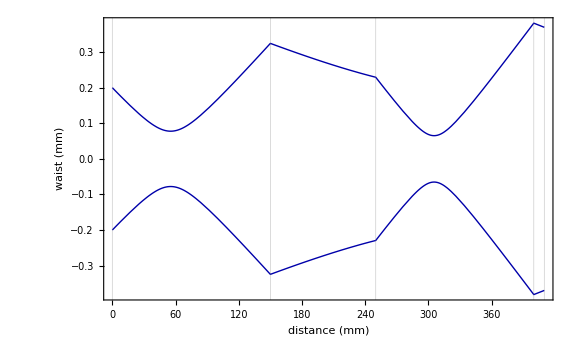

```mathematica
Plot[{waist[z,elements],-waist[z,elements]},{z,0,elements[[-1,2]]},PlotStyle->{{Thick,Darker[Blue]},{Thick,Darker[Blue]}},Frame->True, GridLines->{elements[[All,2]],{}},ImageSize->Large,FrameLabel->{"distance (mm)","waist (mm)"}, PlotRange-> All]
```

```mathematica
elements2={{"Lens",10,75},{"Lens",10+150,75},{"Lens",10+150+100,75},{"Lens",10+150+100+150,75}};
freespace={};
zmax=5000;
λ=813*10^-6;
inputparms2={w0->waist[elements[[-1,2]],elements],R0->rcurv[elements[[-1,2]],elements]};(*input waist and curvature in mm*)
lim = 5;
q0recip2=1/R0-ⅈ λ/(π w0^2)/.inputparms2;
z02=(π w0^2)/λ/.inputparms2;
qrecip2[z_,optics_]:=(abcd[z,optics][[2,1]]+abcd[z,optics][[2,2]]*q0recip2)/(abcd[z,optics][[1,1]]+abcd[z,optics][[1,2]]*q0recip2)
rcurv2[z_,optics_]:=(Re[qrecip2[z,optics]])^-1
waist2[z_,optics_]:=(-(Im[qrecip2[z,optics]]*π)/λ)^(-1/2)
```

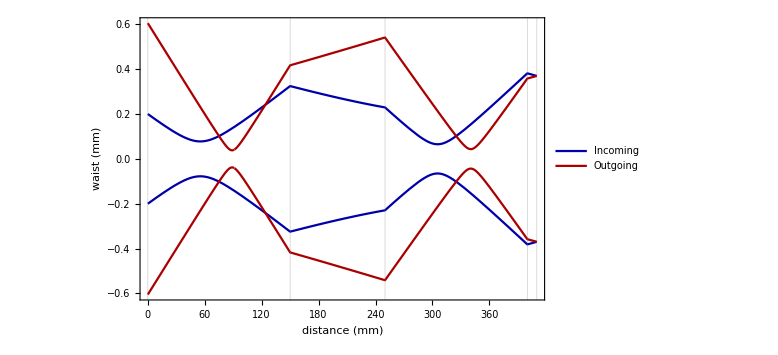

```mathematica
Plot[{waist[z,elements],-waist[z,elements], waist2[elements2[[-1,2]]-z,elements2],-waist2[elements2[[-1,2]]-z,elements2]},{z,0,elements2[[-1,2]]},PlotStyle->{{Thick,Darker[Blue]},{Thick,Darker[Blue]},{Thick,Darker[Red]},{Thick,Darker[Red]}},Frame->True, GridLines->{elements[[All,2]],{}},ImageSize->Large,FrameLabel->{"distance (mm)","waist (mm)"}, PlotRange-> All,PlotLegends->{"Incoming",None,"Outgoing",None}]
```

```mathematica
rcurv[250+75,elements]//N
R=rcurv2[elements2[[-1,2]]-(250+75),elements2]//N
```

33.3601

18.837

```mathematica
rmax  = √(R^2-(R-λ/2)^2) ;(* rmax given phase in mm *)
rmax/(wh0*10^3)
```

1.23751

```mathematica
5*300/6.24
```

240.385